Wolfram Online Mini Campus. Part 13

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 13

Surfaces as Creativity Reflections

```mathematica
f=Log[1+θ]Sin[5ϕ]-Cos[2θ]Floor[2ϕ];
SphericalPlot3D[f,{θ,0,2Pi},{ϕ,0,2Pi},ImageSize->Large,PlotRange->All,PlotPoints->15,
                                     Mesh->False,Boxed->False,Axes->False,PlotStyle->Opacity[0.8],ExclusionsStyle->{None,Gray},
              ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["BrightBands"][.8-r]]]
```

-Graphics3D-

```mathematica
Table[SphericalPlot3D[Log[2-Sin[T*θ]]ϕ,{θ,0,2Pi},{ϕ,0,2 Pi},Boxed->False,Axes->False,
       PlotRange->All,PlotPoints->30,NormalsFunction->None,PlotStyle->Opacity[.9],Mesh -> None,
       ColorFunction ->Function[{x,y,z,θ,ϕ,r},ColorData["CoffeeTones"][RandomReal[{0,1}]]]],{T,{1,11}}]
```

{-Graphics3D-,-Graphics3D-}

Areas as Creativity Reflections

```mathematica
L1=Prepend[Append[Table[{.5+.005*i,1.1+Sin[.03*i]},{i,200}],{2,0}],{0,0}];
L2={{0,0},{.5,2.3},{1.5,2.3},{2,0},{0,0}};
Show[Graphics[{Texture[ExampleData[{"ColorTexture","MultiSpiralsPattern"}]], Polygon[L2,VertexTextureCoordinates ->L2],
                         Style[Line[L2],RGBColor["silver"],Thickness[.015]],Style[Polygon[L1],RGBColor["#3636ff"]],
           Style[Line[L1],RGBColor["silver"],Thickness[.015]]}],PlotPoints->100]
```

-Graphics-

```mathematica
ColTab=Table[RGBColor[col],{col,{"#FD5B78","#3366FF","#EE34D2","#50BFE6","#FF6037","#66FF66",
                                                                              "#FFFF66","#FF6EFF","#FFCC33","#AAF0D1","#FF00CC","#CCFF00"}}]
GPP[t_]:=Graphics3D[{Opacity[.7],EdgeForm[None],
                                               Polygon[Table[{(13-t/2) Cos[2Pi k/(13-t)],(13-t/2) Sin[2 Pi k/(13-t)],3t},{k,13-t}], 
                                            VertexColors->Table[ColTab[[k]],{k,13-t}]]}];
Show[Table[GPP[i],{i,Range[1,10,3]}],Boxed->False]
```

{RGBColor[0.9921568627450981, 0.3568627450980392, 0.47058823529411764],RGBColor[0.2, 0.4, 1.0],RGBColor[0.9333333333333333, 0.20392156862745098, 0.8235294117647058],RGBColor[0.3137254901960784, 0.7490196078431373, 0.9019607843137255],RGBColor[1.0, 0.3764705882352941, 0.21568627450980393],RGBColor[0.4, 1.0, 0.4],RGBColor[1.0, 1.0, 0.4],RGBColor[1.0, 0.43137254901960786, 1.0],RGBColor[1.0, 0.8, 0.2],RGBColor[0.6666666666666666, 0.9411764705882353, 0.8196078431372549],RGBColor[1.0, 0.0, 0.8],RGBColor[0.8, 1.0, 0.0]}

-Graphics3D-

Curves as Art Objects

```mathematica
PS[n_,m_]=Table[{ColorData["Rainbow"][i/600],Text["♗",{n* Cos[i* Pi/300]+m *Cos[n*i*Pi/600],
                                n *Sin[i*Pi/300]-m*Sin[n*i*Pi/600]}]},{ i,600}];
Manipulate[Graphics[PS[N,M],ImageSize->Large],{N,Range[30,12,-6]},{M,Range[21,12,-3]}]
```

Graphs as Art Objects

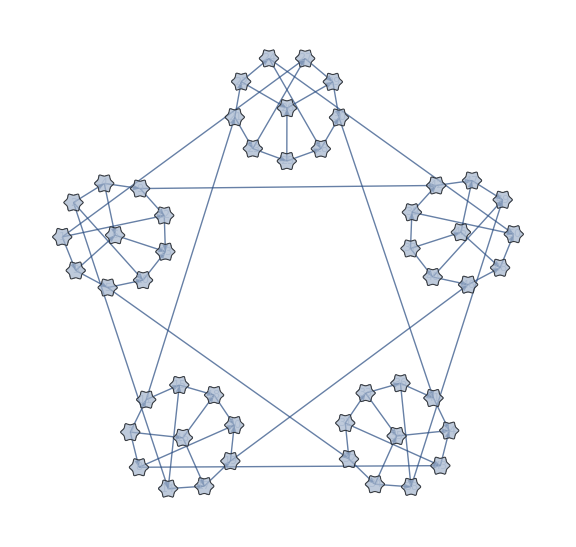

```mathematica
CET=Flatten[Table[Table[i<->j->ColorData["BrightBands"][i/Length[GraphData["SzekeresSnark","Vertices"]]],
                     {j,AdjacencyList[GraphData["SzekeresSnark"],i]}],{i,GraphData["SzekeresSnark","Vertices"]}]];
GraphPlot[GraphData["SzekeresSnark"],ImageSize->Large,EdgeStyle->CET,EdgeShapeFunction->"CarvedArcArrow",
                      VertexStyle->{RGBColor["Silver"],Opacity[0.7]},VertexShapeFunction->"ConcaveHexagon",
                      VertexLabels->Placed[Automatic,{.5,.5}],VertexSize->.5]
```

Derivatives as Processing Objects

```mathematica
FL={{{x*Cos[u]*z^2-y,x^3*u*v^6-Sin[w*t]},{t*Tan[u*w],Exp[y]*z*u-w}},
     {{y^3*v^5-t,x*Log[w]*z^4},{x-Exp[z]*w^7,y*t^8*u*v}}}; FL//MatrixForm
Multicolumn[Table[MatrixForm[D[FL,var]]->var,{var,{x,y,z,u,v,w}}],2]
```

((-y+x z^2 Cos[u]
u v^6 x^3-Sin[t w]) | (t Tan[u w]
-w+ⅇ^y u z)
(-t+v^5 y^3
x z^4 Log[w]) | (-ⅇ^z w^7+x
t^8 u v y))

((z^2 Cos[u]
3 u v^6 x^2) | (0
0)
(0
z^4 Log[w]) | (1
0))→x | ((-x z^2 Sin[u]
v^6 x^3) | (t w Sec[u w]^2
ⅇ^y z)
(0
0) | (0
t^8 v y))→u
((-1
0) | (0
ⅇ^y u z)
(3 v^5 y^2
0) | (0
t^8 u v))→y | ((0
6 u v^5 x^3) | (0
0)
(5 v^4 y^3
0) | (0
t^8 u y))→v
((2 x z Cos[u]
0) | (0
ⅇ^y u)
(0
4 x z^3 Log[w]) | (-ⅇ^z w^7
0))→z | ((0
-t Cos[t w]) | (t u Sec[u w]^2
-1)
(0
(x z^4)/w) | (-7 ⅇ^z w^6
0))→w

HTML as Processing Objects

```mathematica
EmbeddedHTML[" <style>@import url('https://fonts.googleapis.com/css?family=Ewert'); polygon {fill:#eeeeee; stroke:#3636ff; stroke-width:3; fill-rule:evenodd;};</style> <script>function myFunction() {document.getElementById('demo').innerHTML='Hello, World!';}</script> <svg style='background-color:aliceblue;' height='210' width='200'> <polygon onclick='myFunction();' points='100,10 40,198 190,78 10,78 160,198'/> <p style='color:#3636ff; font-family:Ewert; font-size:150%;' id='demo'></p></svg>",
ImageSize->{300,300}]
```

Null <style>@import url('https://fonts.g…font-size:150%;' id='demo'></p></svg> <style>@import url('https://fonts.googleapis.com/css?family=Ewert'); polygon {fill:#eeeeee; stroke:#3636ff; stroke-width:3; fill-rule:evenodd;};</style> <script>function myFunction() {document.getElementById('demo').innerHTML='Hello, World!';}</script> <svg style='background-color:aliceblue;' height='210' width='200'> <polygon onclick='myFunction();' points='100,10 40,198 190,78 10,78 160,198'/> <p style='color:#3636ff; font-family:Ewert; font-size:150%;' id='demo'></p></svg>